# Quantum circuit into Amazon Braket

Interact with Amazon Braket through AWS service connection

## Example Content

From a Wolfram notebook, one can interact with Amazon Braket using AWS service connection, sending quantum tasks and getting results. Note since some of Amazon Braket functionalities are Python-based, you need to configure your system to evaluate external Python code, in order to use Python-related functionalities of Wolfram quantum framework.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Make sure that qiskit and amazon-braket-sdk are installed

```mathematica
ResourceFunction["PythonPackageInstalledQ"]["qiskit"]
ResourceFunction["PythonPackageInstalledQ"]["amazon-braket-sdk"]
```

True

True

If needed, use ResourceFunction["PythonPackageInstall"][...] to install packages.

Create a quantum circuit object:

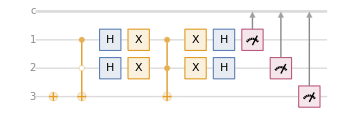

```mathematica
qc=QuantumCircuitOperator[{{"Grover",!a||b},{1},{2},{3}}];
qc["Flatten"]["Diagram"]
```

Get the measurement probabilities:

```mathematica
meas=qc[]["Probabilities"]
```

<|000→1/16,001→9/16,010→1/16,011→1/16,100→1/16,101→1/16,110→1/16,111→1/16|>

Generate OPENQASM3 of the circuit, using AWSBraket:

```mathematica
qasmAWS=qc["Qiskit"]["QASM","Provider"->"AWSBraket"]
```

OPENQASM 3.0;
qubit[3] q;
x q[1];
v q[2];
v q[2];
h q[2];
cnot q[1], q[2];
ti q[2];
cnot q[0], q[2];
t q[2];
cnot q[1], q[2];
t q[1];
ti q[2];
cnot q[0], q[2];
cnot q[0], q[1];
t q[0];
ti q[1];
cnot q[0], q[1];
h q[0];
x q[0];
x q[1];
h q[1];
x q[1];
t q[2];
h q[2];
h q[2];
cnot q[1], q[2];
ti q[2];
cnot q[0], q[2];
t q[2];
cnot q[1], q[2];
t q[1];
ti q[2];
cnot q[0], q[2];
cnot q[0], q[1];
t q[0];
ti q[1];
cnot q[0], q[1];
x q[0];
h q[0];
x q[1];
h q[1];
t q[2];
h q[2];
#pragma braket result probability q[2], q[0]
#pragma braket result probability q[1]
#pragma braket result probability q[0], q[2]

Generate OPENQASM3, given a specific backend on AWSBraket:

```mathematica
qc["Qiskit"]["QASM","Provider"->"AWSBraket","Backend"->"Harmony"]
```

OPENQASM 3.0;
qubit[3] q;
x q[1];
ry(-3.141592653589793) q[2];
rz(-3.141592653589793) q[2];
h q[2];
cnot q[1], q[2];
ti q[2];
cnot q[0], q[2];
t q[2];
cnot q[1], q[2];
t q[1];
ti q[2];
cnot q[0], q[2];
cnot q[0], q[1];
t q[0];
ti q[1];
cnot q[0], q[1];
h q[0];
x q[0];
x q[1];
h q[1];
x q[1];
t q[2];
h q[2];
h q[2];
cnot q[1], q[2];
ti q[2];
cnot q[0], q[2];
t q[2];
cnot q[1], q[2];
t q[1];
ti q[2];
cnot q[0], q[2];
cnot q[0], q[1];
t q[0];
ti q[1];
cnot q[0], q[1];
x q[0];
h q[0];
x q[1];
h q[1];
t q[2];
h q[2];
#pragma braket result probability q[2], q[0]
#pragma braket result probability q[1]
#pragma braket result probability q[0], q[2]

Connect to AWS using your credentials (using Access Key ID, and Secret Access Key), and execute S3:

```mathematica
s3=ServiceExecute["AWS","GetService",{"Name"->"S3"}]
```

ServiceObject[…]

Execute Amazon Braket on AWS:

```mathematica
braket=ServiceExecute["AWS","GetService",{"Name"->"Braket"}]
```

ServiceObject[…]

Fetch available devices:

```mathematica
devices=braket["SearchDevices","Filters"->{}]["Devices",All]
```

Select SV1, which is a simulator:

```mathematica
sim=devices[SelectFirst[#DeviceArn=="arn:aws:braket:::device/quantum-simulator/amazon/sv1"&],MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

Send a quantum task to SV1 simulator:

```mathematica
taskSV1=braket["CreateQuantumTask",
"DeviceArn"->sim["DeviceArn"],
"DeviceParameters"->{},
"OutputS3Bucket"->"PUT_S3_BUCKET_HERE","OutputS3KeyPrefix"->"tasks",
"Shots"->100,"Action"-><|"braketSchemaHeader"-><|"name"->"braket.ir.openqasm.program","version"->"1"|>,
"source"->qasmAWS|>,
"ValidateRequest"->False,"RequestRegion"->"us-east-1"];
```

Get detailed information on a task:

```mathematica
braket["GetQuantumTask","QuantumTaskArn"->taskSV1["QuantumTaskArn"],"RequestRegion"->"us-east-1"]
```

As one can see, the status of SV1 task is “COMPLETED”.

Find the path of completed task:

```mathematica
outputPathSV1=braket["GetQuantumTask","QuantumTaskArn"->taskSV1["QuantumTaskArn"],"RequestRegion"->"us-east-1"]["OutputS3Directory"];
```

Get the result from Amazon Braket:

```mathematica
resultsSV1=ImportByteArray[s3["GetObject","Bucket"->"amazon-braket-wolfram-mads","Key"->FileNameJoin[{outputPathSV1,"results.json"}],"RequestRegion"->"us-east-1"]["Body"],"RawJSON"]["measurements"];
```

From SV1 results, one can calculate the probabilities:

```mathematica
probSV1=N@Normalize[KeySort@Join[AssociationThread[Tuples[{0,1},3],0],Counts@resultsSV1],Total]
```

<|{0,0,0}→0.05,{0,0,1}→0.56,{0,1,0}→0.06,{0,1,1}→0.05,{1,0,0}→0.07,{1,0,1}→0.04,{1,1,0}→0.08,{1,1,1}→0.09|>

Visualize SV1 results vs Wolfram quantum framework predictions:

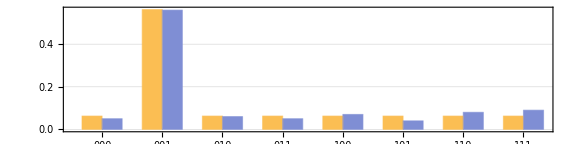

```mathematica
BarChart[Transpose[Values/@{meas,probSV1}],ChartLabels->{Keys[meas],None},BarSpacing->{0,1},ChartLegends->Placed[{"Wolfram Quantum Framework","Amazon Braket SV1"},Center],GridLines->Automatic,AspectRatio->1/4,ImageSize->Large,Frame->True]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Amazon Braket

AWS service connection

Quantum circuit

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.